```mathematica
Lecture 7:Graphics
```

## Plotting lists and matrices

### Exercise Subsection

The Conway recursive sequence is defined by the following cell:

```mathematica
Clear[a]
a[n_]:=a[n]=If[n<=2,1,a[a[n-1]]+a[n-a[n-1]]]
```

Use ListPlot to plot the list of terms of the form a[n]/n where n ranges from 1 to 10000.

### Exercise Subsection

Illustrate that the number of primes numbers <= n grows approximately at the same rate as the function n/Log[n] by plotting the list of terms of the form PrimePi[n]/(n/Log[n]) for n = 2,...,10^5 and observing that the terms approach a limiting value.

### Exercise Subsection

Define the Mobius function mu on the integers such that mu[n] is equal to +1 if n is square free (meaning no square number divides n, see SquareFreeQ) and has an even number of prime factors, -1 if n is squarefree with an odd number of prime factors, and 0 otherwise.  

The Mertens function is defined to send the integer n>=2 to mu[2] + ... + mu[n].  Use ListPlot to plot the first 5000 values of the Mertens function.

### Exercise Subsection

Use MatrixPlot to plot the matrix M[n] for various inputs n where M[n] is the matrix defined by the following cell:

```mathematica
M[n_]:=Table[Mod[Binomial[i,j],2],{i,0,n},{j,0,n}]
```

## Plotting in 2D

```mathematica
Plot,ContourPlot,ParametricPlot,Show, Options,RegionPlot
```

### Exercise Subsection

Compare the graphs of 1-π/2+(4 Cos[x])/π+(4 Cos[3 x])/(9 π)+(4 Cos[5 x])/(25 π)+(4 Cos[7 x])/(49 π) and 1-Abs[x] by using Plot to plot these functions on the same axes.

### Exercise Subsection

Use Plot to show the graphs of Sin[n x]/x on the interval from -Pi to Pi for values of n=1,2,...,5 all on the same axes.

### Exercise Subsection

Use ParametricPlot to show plot the curve described by the parametric equations defined in the next cell.

```mathematica
f[t_]:=(E^Cos[t] - 2 Cos[4 t]-Sin[t/12]^5);
x[t_]:=Sin[t] f[t];
y[t_]:=Cos[t]f[t];
```

### Exercise Subsection

What does the following cell do when evaluated?

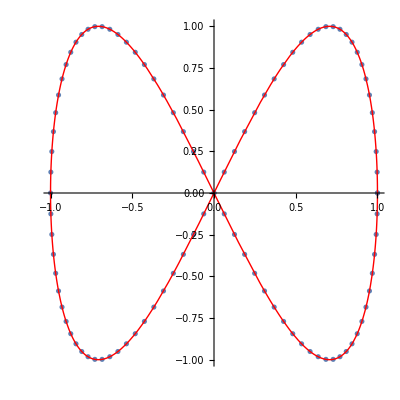

```mathematica
G1=ListPlot[{Cos[#], Sin[2 #]}&/@Range[0,2 Pi,Pi/50],AspectRatio->1];
G2=ParametricPlot[{Cos[t],Sin[2 t]},{t,0,2Pi},PlotStyle->{Red,Thin}];
Show[G1,G2]
```

### Exercise Subsection

Use ContourPlot to graph the (x,y) coordinate pairs that satisfy Abs[3x^2 + x y^2 - 2] == Abs[x^2 - y^2 + 4].

### Exercise Subsection

Use ContourPlot to graph the (x,y) coordinate pairs that make the function (x^2 + Sin[Pi y])^3 equal to the function (x + Cos[2 Pi y)^2.

### Exercise Subsection

Use RegionPlot to graph the (x,y) coordinate pairs that satisfy Abs[x^2 + y] <= Abs[x + y^2].

## Plotting in 3D

```mathematica
Plot3D,ContourPlot3D,ParametricPlot3D
```

### Exercise Subsection

Compare the Plot3D and the ContourPlot output for the function x Sin[x^2 + y^2]/(x^2 + y^2), playing with the Contours and PlotPoints options for ContourPlot.

### Exercise Subsection

```mathematica
ParametricPlot3D[{Cos[t]Sin[t],Cos[2 t],Sin[3t]},{t,0,3Pi}]
```

-Graphics3D-

### Exercise Subsection

Use ContourPlot3D to plot the points in R^3 that satisfy (x^2 + (9/4) y^2 + z^2 - 1)^3 - x^2 z^3 - 9 y^2 z^3/80 equalling 0.  Play with the Options in ContourPlot3D, considering adjusting Mesh, Boxes, Axes, and PlotPoints.

```mathematica
ContourPlot3D[(x^2 + (9/4) y^2 + z^2 - 1)^3 - x^2 z^3 - 9 y^2 z^3/80==0,{x,-2,2},{y,-2,2},{z,-2,2},Mesh->ScreenArea,Boxed->False,Axes->False,PlotPoints->50]
```

Mesh::ilevels: ScreenArea is not a valid mesh specification.

-Graphics3D-

```mathematica
?Mesh
```

## Graphics objects

### Exercise Subsection

Use Graphics to draw all of these objects in the same image: 
a. a Red Line that connects the points {0,0}, {1,1}, {1,0}, {0,1}, 
b. a Green Circle with center at {.5,.5} and radius .5, 
c. a Purple Arrow that connects the points {0,0}, {0,1}, and 
d. a Orange Point with PointSize .1 at {.5,.5}.

### Exercise Subsection

Use Graphics together with Line to draw the ‘g-raph’ created by the line segments that pass through the {x,y} coordinates in the next cell:

```mathematica
coordinates={{12,-536},{32,-528},{52,-512},{64,-496},{72,-472},{80,-452},{88,-436},{96,-416},{108,-396},{120,-376},{132,-352},{140,-332},{144,-308},{140,-288},{132,-264},{136,-260},{152,-280},{160,-300},{168,-324},{164,-344},{168,-368},{168,-388},{168,-412},{168,-432},{164,-456},{156,-476},{148,-492},{124,-504},{128,-520},{152,-524},{168,-516},{184,-500},{192,-480},{192,-456},{192,-432},{196,-408},{200,-388},{200,-364},{204,-340},{204,-320},{204,-296},{200,-272},{192,-256},{180,-236},{172,-216},{168,-192},{168,-172},{172,-148},{176,-124},{176,-104},{184,-96},{188,-116},{192,-140},{192,-164},{196,-184},{200,-208},{204,-228},{208,-252},{212,-272},{212,-296},{216,-320},{220,-340},{232,-352},{240,-332},{240,-312},{240,-288},{236,-264},{228,-244},{216,-220},{216,-196},{212,-176},{212,-152},{208,-128},{208,-108},{204,-84},{196,-64},{184,-44},{168,-28},{152,-16},{136,0},{116,8},{96,20},{76,28},{56,36},{36,48},{20,64},{4,80},{-12,96},{-20,116},{-32,136},{-40,156},{-52,176},{-64,192},{-80,208},{-80,232},{-80,252},{-84,276},{-88,296},{-88,320},{-88,340},{-88,364},{-84,384},{-80,408},{-80,432},{-68,452},{-44,456},{-20,456},{-4,468},{-16,484},{-40,492},{-36,508},{-32,528},{-52,528},{-68,516},{-88,524},{-108,536},{-132,540},{-152,540},{-172,548},{-192,560},{-216,564},{-232,544},{-216,524},{-196,516},{-180,504},{-172,484},{-156,464},{-148,444},{-144,424},{-144,400},{-148,380},{-156,356},{-164,332},{-172,312},{-176,288},{-176,264},{-184,244},{-188,220},{-188,196},{-188,176},{-184,152},{-180,128},{-176,108},{-176,84},{-176,60},{-180,40},{-192,16},{-196,-8},{-188,-28},{-172,-52},{-160,-76},{-152,-96},{-148,-120},{-152,-144},{-156,-164},{-156,-188},{-156,-212},{-156,-232},{-156,-256},{-164,-280},{-168,-300},{-172,-324},{-172,-348},{-176,-368},{-176,-392},{-184,-416},{-188,-436},{-192,-456},{-200,-480},{-212,-496},{-228,-508},{-236,-528},{-216,-536},{-196,-524},{-180,-508},{-168,-488},{-160,-468},{-156,-444},{-152,-420},{-148,-400},{-140,-376},{-140,-356},{-136,-332},{-124,-308},{-120,-284},{-112,-280},{-112,-304},{-108,-324},{-104,-348},{-100,-372},{-96,-392},{-96,-416},{-96,-440},{-96,-460},{-100,-484},{-120,-508},{-124,-524},{-96,-528},{-80,-512},{-76,-492},{-64,-468},{-64,-444},{-64,-424},{-68,-400},{-72,-376},{-76,-352},{-76,-332},{-76,-308},{-76,-284},{-76,-264},{-80,-240},{-80,-216},{-84,-196},{-84,-172},{-84,-148},{-64,-148},{-40,-148},{-16,-152},{4,-148},{24,-152},{32,-176},{40,-192},{52,-212},{60,-232},{72,-252},{80,-272},{88,-288},{92,-312},{92,-332},{88,-352},{84,-372},{76,-396},{64,-416},{56,-436},{44,-460},{36,-476},{24,-492},{8,-508},{-12,-520},{-12,-536},{12,-536}};
```

### Exercise Subsection

A turtle (see https://en.wikipedia.org/wiki/Turtle_graphics ) takes a random walk of length n in the the plane.  The turtle begins at {0,0} pointing East and then repeats the following steps n times: 

1. the turtle randomly selects a radian angle between 0 and 2Pi and then rotates that angle (relative to its current position).
2. the turtle takes one step forward. 

Use AnglePath together with Line and Graphics to draw one such random walk of length 10000.  Your graphics image should include the x and y Axes.

### Exercise Subsection

Recall from Exercise Set 5 that Thue-Morse sequence is a sequence of lists that begins with the list {0} and then subsequent terms in the sequence are found by replacing each 0 in the previous list with 0, 1 and each 1 with 1, 0.  It can be defined using the function in the next cell:

```mathematica
tm[n_]:=Nest[Flatten[#/.{0->{0,1},1->{1,0}}]&,{0},n]
```

Turn tm[n] into a graphic in the plane using AnglePath together with Line and Graphics in the following way.  Beginning at the {0,0} pointing East, turn right (using angle -Pi/3) and travel one step forward for each 1 in tm[n] and go straight (using angle 0) and travel one step forward for each 0 in tm[n].  Show the graphic created in this way when n=15.

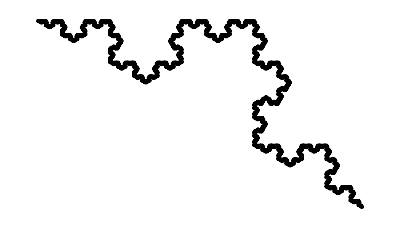

```mathematica
Graphics@Line@AnglePath[tm[15]/.{1->-Pi/3}]
```

### Exercise Subsection

The regular paperfolding sequence (see https://en.wikipedia.org/wiki/Regular_paperfolding_sequence or https://en.wikipedia.org/wiki/Dragon_curve ) is a sequence of bit strings.  The paperfolding sequence can be defined recursively with Paper[0] = {1} and then taking Paper[n] to be the list created by Join-ing the list Paper[n-1], the list {1}, and the list Paper[n-1] in reverse order with each 1 replaced with a 0 and each 0 replaced with a 1.

a. Define the function Paper[n]

b. Turn Paper[n] into a graphic in the plane using AnglePath in together with Line and Graphics (see the documentation for AnglePath for an example).  Beginning at the {0,0}, turn right (using angle -Pi/2) and travel one step forward for each 1 in Paper[n] and turn left (using angle Pi/2) and travel one step forward for each 0 in Paper[n].  Show the graphic created in this way when n=12.

```mathematica
Paper[n_]:=If[n==0,{1},Join[Paper[n-1],{1},Reverse@Paper[n-1]/.{1->0,0->1}]]
```

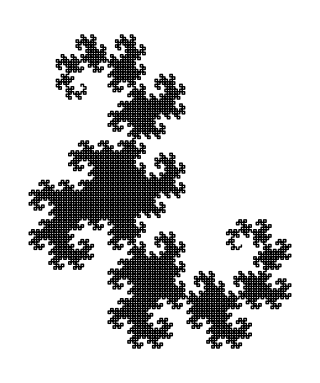

```mathematica
Graphics@Line@AnglePath[Paper[12]/.{1->-Pi/2,0->Pi/2}]
```

### Exercise Subsection

## Animations

```mathematica
Animate, ListAnimate, Manipulate
```

### Exercise Subsection

Use Manipulate to vary the parameters a to investigate the graphs of the parametric curves described by

```mathematica
{a Cos[t]+(1-a) Sin[2 t],a Sin[t]+(1-a) Cos[3 t] Sin[t]}
```

where t can vary from 0 to 2Pi and a from 0 to 1.

### Exercise Subsection

The fundamental theorem of algebra says that every nonconstant polynomial f[x] has a complex root; meaning that there is a complex c such that f[c]=0.  Every complex number c can be expressed in polar form as c = r E^(i t) where r is a positive number and t is an angle between 0 and 2 Pi.  Therefore the fundamental theorem of algebra says there is a positive r and a t between 0 and 2 Pi for which both the real and imaginary parts of f[r E^(i t)] is equal to 0. 

Explain how the below cell can be used to illustrate the validity of the fundamental theorem of algebra for the given polynomial f[x].

```mathematica
f[x_]:=x^3+x^2-x+1;
Manipulate[ParametricPlot[{Re[f[r E^(I t)]],Im[f[r E^(I t)]]},{t,0,2Pi},PlotRange->{-5,5},AspectRatio->1],{r,0,3}]
```

### Exercise Subsection

```mathematica
SecantLine[f_,x_,h_]:=Graphics[{Red,Thickness[.002],InfiniteLine@{{x,f[x]},{x+h,f[x+h]}}}]
SecantPoints[f_,x_,h_]:=Graphics[{Red,PointSize[.01],Point[{x,f[x]}],Point[{x+h,f[x+h]}]}]
f[x_]:=Cos[x]
```

```mathematica
Manipulate[Show[
Plot[f[x],{x,-Pi,Pi},PlotRange->{-2,2},AspectRatio->1],
SecantLine[f,0,h],
SecantPoints[f,0,h]
],{h,3,.001,.1}]
```

### Exercise Subsection

Let M be a 20x20 matrix (a list of 20 lists, each of length 20) with entries either 0 or 1.

The neighbors of an i,j entry in M are the entries in M that are horizontally, vertically, or diagonally adjacent to the i,j entry.  An entry usually has 8 neighbors unless the entry is in a row or column on the border of M, in which case there can be fewer neighbors. 

a. Define a function Neighbors[M_,{i_,j_}] that inputs a 20x20 matrix M, a row i, and a column j, and outputs the number of neighbors of the i,j entry in M that are equal to 1.

Conway’s game of life is a function that changes M according to the following rules:
1. If an entry in M is 1 and has fewer than two neighbors equal to 1, then the entry changes to 0.
2. If an entry in M is 1 and has more than three neighbors equal to 1, then the entry changes to 0.
3. If an entry is 0 and has exactly three neighbors equal to 1, then the entry changes to 1. 
4. All other entries are unchanged.

b. Define a function Conway[Mat_] that transforms Mat using the above rules.

c. Try the command ListAnimate[ArrayPlot/@NestList[Conway,M,100]] where StartM is the matrix in the next cell.  Then change StartM to another matrix of your invention to produce another cool looking “movie”.

```mathematica
StartM={{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0}};
```

```mathematica
Neighbors[M_,{i_,j_}]:=Count[M[[First@#,Last@#]]&/@DeleteCases[{i,j}+#&/@DeleteCases[Tuples[{-1,0,1},2],{0,0}],{a_,b_}/;Or[a==0,b==0,a==21,b==21]],1]
Conway[M_]:=Table[
Which[And[M[[i,j]]==1,Neighbors[M,{i,j}]<2],0,
And[M[[i,j]]==1,Neighbors[M,{i,j}]>3],0,
And[M[[i,j]]==0,Neighbors[M,{i,j}]==3],1,
True,M[[i,j]]],{i,20},{j,20}]
```

```mathematica
ListAnimate[MatrixPlot/@NestList[Conway,StartM,100]]
```